# Report Project 3

Course code: IX1500 - Discrete Mathematics
Date: 2017-10-10

Evan Saboo, saboo@kth.se

Task Level C: Graph Application

## Summary

### Task

Every city listed below represents a router that forwards packet to their final destination. The weight (cost) between two linked cities is assumed to be inversely proportional to the free capacity of the link.

This task is about creating an optimal tree so that each router can be accessed with minimal weight. The tree should show how data packets are routed so that each city can be reached by the information flow that is based on Stockholm.

```mathematica
city={"Abisko","Boden","Falun","Goteborg","Hoganas","Hudiksvall","Jonkoping","Kalmar","Kiruna","Lidkoping","Linkoping","Lulea","Lund","Malmo","Mariestad","Ostersund","Stockholm","Strangnas","Timra","Uppsala","Umea","Varberg","Visby"};
```

```mathematica
links={{15,18},{13,17},{3,16},{6,3},{18,6},{12,2},{15,11},{19,21},{7,8},{19,2},{7,4},{21,17},{17,11},{23,11},{10,7},{16,17},{10,20},{13,5},{3,17},{7,22},{15,10},{16,18},{11,16},{17,23},{18,17},{20,6},{11,7},{9,2},{3,20},{4,17},{19,17},{7,20},{22,4},{14,7},{15,17},{6,17},{20,5},{16,15},{11,3},{9,1},{4,10},{5,14},{6,16},{16,19},{13,8},{8,23},{16,10},{4,13},{2,16},{15,3},{20,18}};
```

The list above shows how every city is linked (has an edge) to one or more cities.

```mathematica
city⟦links⟦4⟧⟧
```

{Hudiksvall,Falun}

### Result

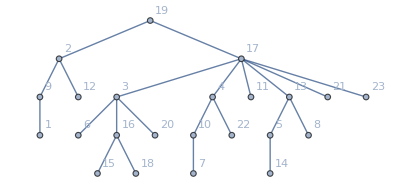
By using Dijkstra’s algorithm (shortest path) we can construct a tree that connect to from Stockholm to every other city with minimal weight (cost).
 
The picture below demonstrates the shortest path spanning tree where every city is presented as its corresponding index number in the “city list” above.  

 -Graphics-

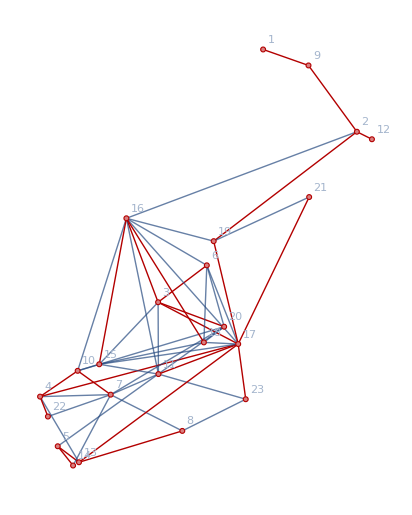
We can illustrate a graph by placing every city in its corresponding coordinates with their connected links. The graph also shows the shortest path spanning tree as highlighted.
-Graphics-

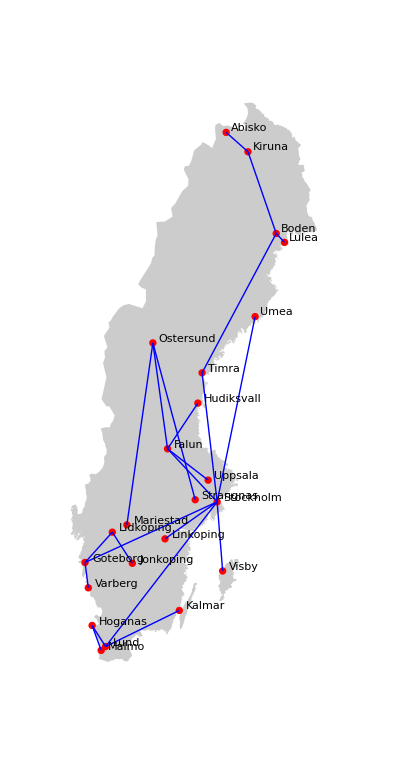
I have also illustrated the shortest path spanning tree with the map of Sweden and its connected cities (routers).  
-Graphics-

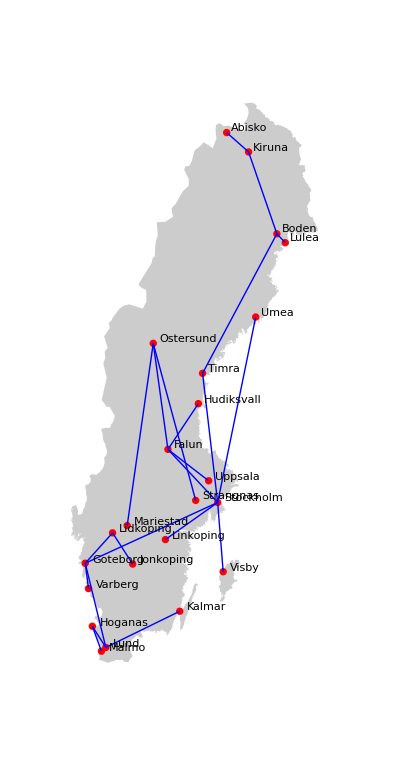
If the link between Stockholm and Lund stops working then the shortest path spanning tree changes. The shortest path from Stockholm to Lund in the new tree is:
 Stockholm → Göteborg → Lund
 -Graphics-

## Routing

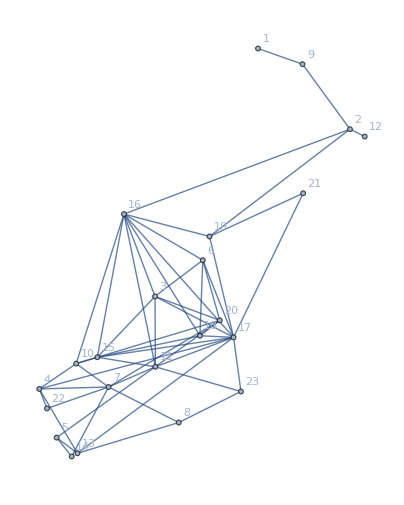
The first thing we need to do is to give every link its own weight (cost).
We do that by dividing a constant with the free capacity of the link.
In this case we suppose that the constant is 1 and the available capacity for each link is:

Stockholm | – | Göteborg | 25
Stockholm | – | Lund | 25
Göteborg | – | Lund | 25
Stockholm | – | Falun | 15
Falun | – | Östersund | 15

The other links have a capacity ranging from 1 to 5 at random. 

Below is the graph presentation of every city (represented by a number) connected with the provided links.
-Graphics-

### Creating shortest path spanning tree

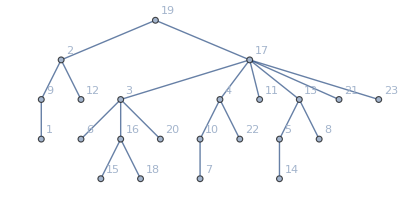
The tree we want to create needs to have the shortest path from Stockholm to every other city. We can compute the shortest path by using Dijkstra’s shortest path algorithm. The algorithm goes through every weighted edge connecting the starting node to the target node and chooses the path with the lowest total weight.
It can also find the shortest path from one vertex to every other vertex to create the shortest path spanning tree, where the starting vertex is the root.

By combining every path we can construct the shortest path spanning tree. The pseudo code below creates a list of links which represents the shortest path spanning tree: 

FindShortestPathTree:
For x=1 to length(amountOfLinks)
	P=Shortest Path From Stockholm to city[x];
		For edge=1 to (length(P)-1)
			if(P[link] is not member of shortestPathTreeList)
			Add P[link] to shortestPathTreeList;
		End for link
End for x
Return shortestPathTreeList

The tree below is the solution we wanted from the code above.
-Graphics-

The reason why Dijkstra’s algorithm was used was because we wanted a spanning tree which guaranteed us the shortest path from a specific vertex to every other connected vertexes. We could have used Kruskal’s algorithm to create a minimum spanning tree but it wouldn’t guarantee us the shortest path from the root vertex to every other vertexes, we would only get a tree whose sum of all edge weights is the smallest possible weight. 

We an also illustrate the shortest path tree with the map of Sweden and its cities:
-Graphics-

### If a link stops working

What will happen if the link between Stockholm and Lund stops working?

When the link stops working the shortest path tree will split up into two subtrees and all routers (cities) in the second subtree will also lose their shortest path to Stockholm,
in other words they would lose the link which connected them to Stockholm.
We now need to find an alternative shortest path for every router not connected to Stockholm.

We will the same algorithm to construct an alternative shortest path spanning tree which does not include the link between Stockholm and Lund:
-Graphics-

We can see above that The shortest path from Stockholm to Lund is now:
Stockholm → Göteborg → Lund
We can also see that the other routers who lost connection to Stockholm now have other shortest paths.

## Code

```mathematica
ClearAll["`*"];
```

```mathematica
city={"Abisko","Boden","Falun","Goteborg","Hoganas","Hudiksvall","Jonkoping","Kalmar","Kiruna","Lidkoping","Linkoping","Lulea","Lund","Malmo","Mariestad","Ostersund","Stockholm","Strangnas","Timra","Uppsala","Umea","Varberg","Visby"};
```

```mathematica
links={{15,18},{13,17},{3,16},{6,3},{18,6},{12,2},{15,11},{19,21},{7,8},{19,2},{7,4},{21,17},{17,11},{23,11},{10,7},{16,17},{10,20},{13,5},{3,17},{7,22},{15,10},{16,18},{11,16},{17,23},{18,17},{20,6},{11,7},{9,2},{3,20},{4,17},{19,17},{7,20},{22,4},{14,7},{15,17},{6,17},{20,5},{16,15},{11,3},{9,1},{4,10},{5,14},{6,16},{16,19},{13,8},{8,23},{16,10},{4,13},{2,16},{15,3},{20,18}};
```

A function to find coordinates of a city.

```mathematica
pos[c_String]:=CityData[c,"Coordinates"];
pos[i_Integer]:=CityData[city⟦i⟧,"Coordinates"]
```

```mathematica
𝕔= pos /@city
```

{{68.349,18.8319},{65.83,21.7},{60.61,15.62},{57.72,12.01},{56.2,12.55},{61.74,17.11},{57.78,14.17},{56.67,16.36},{67.86,20.22},{58.51,13.16},{58.41,15.63},{65.6,22.16},{55.71,13.2},{55.61,13.02},{58.71,13.82},{63.18,14.65},{59.33,18.07},{59.38,17.02},{62.48,17.32},{59.86,17.64},{63.83,20.24},{57.11,12.25},{57.64,18.3}}

Create an adjacency matrix with no connected edges.

```mathematica
n=Length[city];
𝔸=ConstantArray[0,{n,n}];
```

Assign links to connected cities.

```mathematica
setLink[{i_,j_}]:=𝔸⟦i,j⟧=𝔸⟦j,i⟧=1;
```

```mathematica
setLink/@links;
```

A Function which generates a randomized weight for every edge (link).

```mathematica
genWeight[e_, c_]:=
Module[{edgeWeight  = {}, capacity, i},
For[i=0, i<Length[e], i++,
capacity = RandomInteger[{1,5}];
AppendTo[edgeWeight, c/capacity];
];
edgeWeight
]
```

```mathematica
constant = 1;
```

```mathematica
w = genWeight[links, constant]
```

{1,1/4,1/5,1,1/5,1/4,1,1,1,1/3,1/4,1,1/5,1/2,1/5,1/4,1/4,1/3,1/4,1/5,1/2,1/2,1/4,1/5,1/5,1,1,1/3,1/5,1/4,1/4,1/5,1/3,1/3,1/4,1/4,1/3,1/5,1,1/5,1/2,1,1/3,1/3,1/3,1/2,1/4,1/4,1/5,1/5,1/5}

Specific edge-weights.

```mathematica
w[[15]] = constant/25;
w[[39]] = constant/25;
w[[14]] = constant/25;
w[[10]] = constant/15;
w[[9]] = constant/15;
```

Create a graph with the provided adjacency matrix and position the vertexes according to the provided  city coordinates.

```mathematica
𝒢=AdjacencyGraph[𝔸,VertexCoordinates->(Reverse/@𝕔),VertexLabels->Automatic,EdgeWeight->w]
```

-Graphics-

A method that can be used to draw the graph and a map.

```mathematica
r=10×10^3;
```

```mathematica
Options[geoGraph]={
EdgeStyle->Black,VertexStyle->GeoStyling[None],
VertexLabels->None,VertexLabelStyle->Black
};
geoGraph[v_,e_,c_,r_,OptionsPattern[]]:=
Module[{
es=OptionValue[EdgeStyle],vs=OptionValue[VertexStyle],vl=OptionValue[VertexLabels],vls=OptionValue[VertexLabelStyle],
lbl,Δ={0.1,0.3}
},
If[Length[vl]≠Length[v],vl=None];
lbl=If[
vl===None,{},
Join[{vls},MapThread[Text[#1,GeoPosition[#2+Δ],{-1,0}]&,{vl,c}]]
];
Join[
Join[{vs},(GeoDisk[c⟦#1⟧,r]&)/@v],
Join[{es},(GeoPath[{c⟦#1⟦1⟧⟧,c⟦#1⟦2⟧⟧}]&)/@e],
lbl
]
];
```

A Mathematica function which uses Dijkstra’s algorithm (when specified) to find the shortest weighted path from Stockholm to every other city.

```mathematica
g = FindShortestPath[𝒢,17,All, Method-> "Dijkstra"];
```

```mathematica
edges = {};
```

A function that creates a tree with shortest path from root vertex to every other vertexes.

```mathematica
FShortestPath[c_, l_, g_] :=
Module[{edges = {}, ind,i  ,k, val},
For[i= 1, i < Length[c]+1, i++,
ind = g[i];
For[k = 1, k  < Length[ind], k++,
val = {ind[[k]], ind[[k+1]]};
If[MemberQ[edges, val], , AppendTo[edges, val];
]]
];
edges
];
```

```mathematica
edges = FShortestPath[city, links,g]
```

{{17,19},{19,2},{2,9},{9,1},{17,3},{17,4},{17,13},{13,5},{3,6},{4,10},{10,7},{13,8},{17,11},{2,12},{5,14},{3,16},{16,15},{16,18},{3,20},{17,21},{4,22},{17,23}}

```mathematica
An=ConstantArray[0,{n,n}];
```

```mathematica
setLinks[{i_,j_}]:=An⟦i,j⟧=An⟦j,i⟧=1;
```

```mathematica
setLinks/@edges;
```

Create and draw a graph from the matrix containing the shortest path spanning tree.

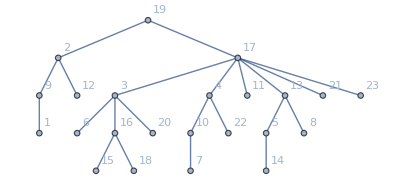

```mathematica
shortestPathTree=AdjacencyGraph[An,VertexLabels->Automatic]
```

Show the original graph with the shortest path spanning tree as highlighted.

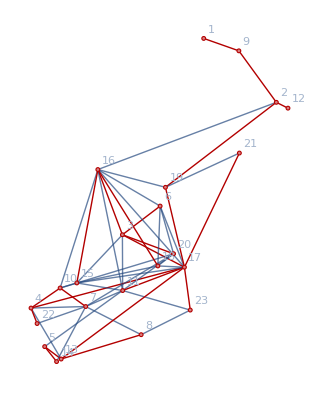

```mathematica
HighlightGraph[𝒢,shortestPathTree,GraphHighlightStyle->"Thick"]
```

```mathematica
v=VertexList[𝒢];
```

Draw the shortest path spanning tree with the map of Sweden.

```mathematica
GeoGraphics[{
Polygon[CountryData["Sweden"]],
geoGraph[v,edges,𝕔,r,EdgeStyle->Blue,VertexStyle->GeoStyling[Red],VertexLabels->city]
},GeoBackground->None,GeoProjection->"LambertAzimuthal"]
```

-Graphics-

Remove the link between Stockholm and Lund from the original graph.

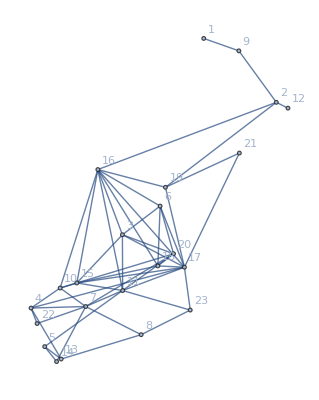

```mathematica
dG =EdgeDelete[𝒢, 13<->17]
```

Construct an alternative shortest path spanning tree while the Stockholm - Lund link is removed.

```mathematica
g2 = FindShortestPath[dG,17,All];
```

```mathematica
edges2 = FShortestPath[city, links,g2]
```

{{17,19},{19,2},{2,9},{9,1},{17,3},{17,4},{4,13},{13,5},{3,6},{4,10},{10,7},{13,8},{17,11},{2,12},{5,14},{3,16},{16,15},{16,18},{3,20},{17,21},{4,22},{17,23}}

Draw the alternative tree with the map of Sweden.

```mathematica
GeoGraphics[{
Polygon[CountryData["Sweden"]],
geoGraph[v,edges2,𝕔,r,EdgeStyle->Blue,VertexStyle->GeoStyling[Red],VertexLabels->city]
},GeoBackground->None,GeoProjection->"LambertAzimuthal"]
```

-Graphics-